```mathematica
S[0][x_] := 1
S[1][x_] := x[[1]]
S[2][x_] := 1/2 x[[1]]^2+x[[2]]
S[3][x_] := 1/6 x[[1]]^3 + x[[1]] * x[[2]] + x[[3]]
S[4][x_] := 1/24 x[[1]]^4 + 1/2 x[[1]] ^2 * x[[2]] + 1/2 x[[2]]^2+x[[1]] * x[[3]] +x[[4]]
S[5][x_] := 1/120 x[[1]]^5 + 1/6 x[[1]]^3 * x[[2]] + 1/2 * x[[1]]*x[[2]]^2+1/2 * x[[1]]^2 *x[[3]] + x[[2]]*x[[3]]+x[[1]]*x[[4]]+x[[5]]
S[6][x_]:=x⟦1⟧^6/720+(x⟦1⟧^4 x⟦2⟧)/24 +(x⟦1⟧^2 x⟦2⟧^2)/4 +x⟦2⟧^3/6+(x⟦1⟧^3 x⟦3⟧)/6 +x⟦1⟧ x⟦2⟧ x⟦3⟧+x⟦3⟧^2/2+(x⟦1⟧^2 x⟦4⟧)/2+x⟦2⟧ x⟦4⟧+x⟦1⟧ x⟦5⟧+x[[6]]
S[7][x_]:=x⟦1⟧^7/5040+(x⟦1⟧^5 x⟦2⟧)/120 +(x⟦1⟧^3 x⟦2⟧^2)/12 +(x⟦1⟧ x⟦2⟧^3)/6 +(x⟦1⟧^4 x⟦3⟧)/24 +(x⟦1⟧^2 x⟦2⟧ x⟦3⟧)/2 +(x⟦2⟧^2 x⟦3⟧)/2+(x⟦1⟧ x⟦3⟧^2)/2+(x⟦1⟧^3 x⟦4⟧)/6+x⟦1⟧ x⟦2⟧ x⟦4⟧+x⟦3⟧ x⟦4⟧+(x⟦1⟧^2 x⟦5⟧)/2+x⟦2⟧ x⟦5⟧+x⟦1⟧ x⟦6⟧+x[[7]]

ss=CoefficientList[ Series[Log[2/p Tanh[p/2]],{p,0,10}],p];
s=Part[ss,{2,3,4,5,6}]
xp[n_][x_, t_] := {x-2ⅈ t + n, 0, (x - 8 ⅈ  t)/(3!)+100,0, (x - 32 ⅈ  t)/(5!)+100}
xn[n_][x_, t_] := {x+2ⅈ t - n, 0, (x + 8 ⅈ  t)/(3!)+100,0, (x + 32 ⅈ  t)/(5!)+100}

M[NN_][n_][x_,t_]:=Table[∑_(ν=0)^Min[i,j] 1/4^ν S[i-ν][xp[n][x,t]+ν s]S[j-ν][xn[n][x,t]+ν s],{i,1,2NN-1,2},{j,1,2NN-1,2}]
τ[k_][x_,t_] := Det[M[3][k][x,t]]
g[x_,t_] := τ[1][x,t]
f[x_,t_] := τ[0][x,t]
gc[x_,t_] := τ[-1][x,t]
u[x_,t_]:= g[x,t]/f[x,t]*Exp[-2ⅈ t]
uc[x_,t_]:= gc[x,t]/f[x,t]*Exp[2ⅈ t]
U = u[x,t]//FullSimplify;
Uc = uc[x,t]//FullSimplify;
eq=-ⅈ D[U,t]+D[U,{x,2}]+2*U^2*Uc//FullSimplify
(*Plot3D[Abs[U],{x,-30,30},{t,-30,30},PlotRange->All,PlotPoints->300,ColorFunction->"BlueGreenYellow",AxesLabel->{Style[x,20],Style[t,20],Style["|u|",20]}]*)
(*p = Animate[Plot[Abs[u[x,t]],{x,-8,8},PlotRange ->{0,3.5},AxesLabel->{"x","|u|"}],{t,-3,3},AnimationRunning ->False]
SetDirectory[NotebookDirectory[]];
Directory[]
Export["3-order-RW.gif",p]*)
(*ⅈ D[u,t]-D[u,{x,2}]-2 uc* u^2 //FullSimplify*)
(*DensityPlot[Abs[U],{x,-15,15},{t,-10,10},ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,PlotPoints->200, PlotRange->All,AxesLabel->{"x","t"}]*)
Plot[{Abs[U]/.{t->-5.08},Abs[U]/.{t->0},Abs[U]/.{t -> 2.75},Abs[U]/.{t -> 5.08},Abs[U]/.{t -> -2.75}},{x,-30,30},PlotRange->{0,5},AxesLabel->{"x","|u|"},PlotStyle->{Thick,Dashed,Thick,Dashed,Thick},PlotLegends->Placed[{"t = -5.08","t = 0","t = 2.75","t = 5.08","t = -2.75"},{0.65,0.3}]]
(*M[3][k][x,t]*)
```

{0,-1/12,0,7/1440,0}

0

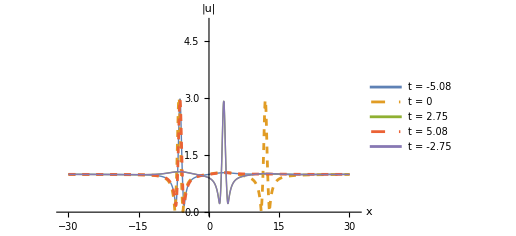

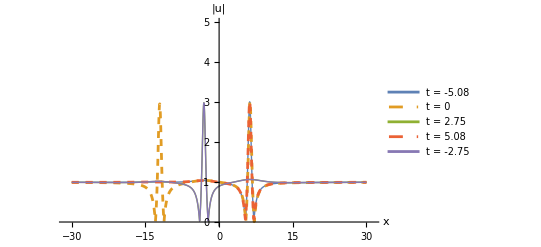

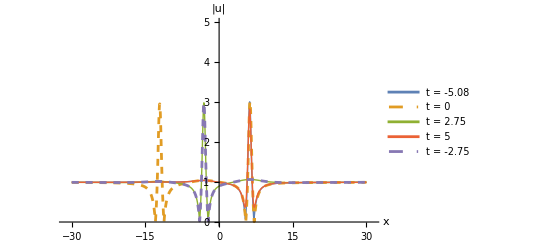

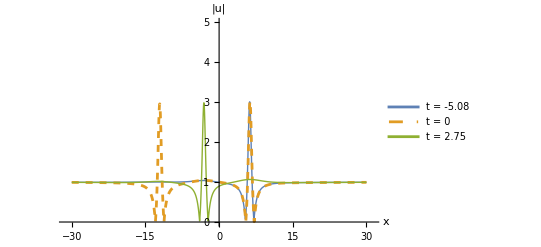

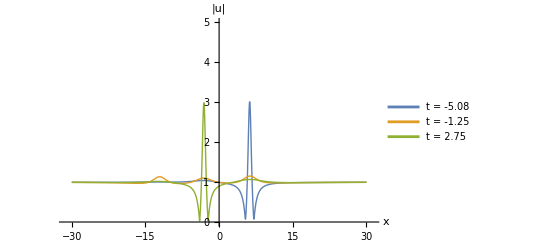

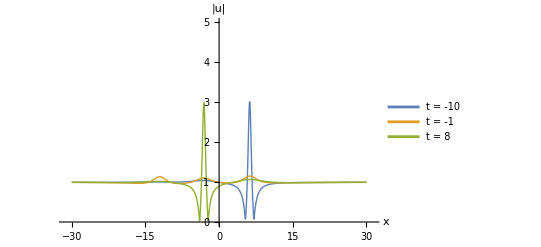

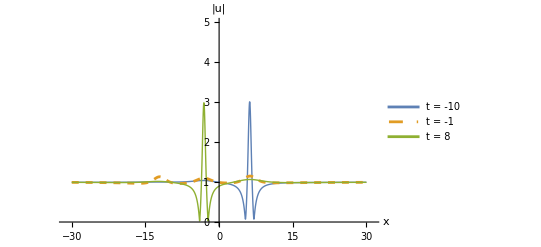

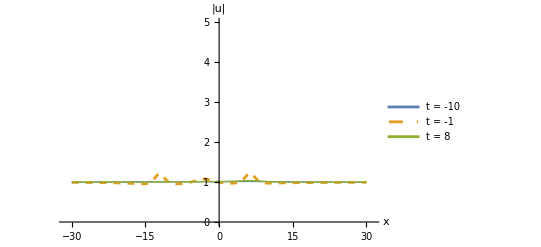

```mathematica
U
```

(ⅇ^(-2 ⅈ t) (2025 (409599359993-10240035200 x)+8 (4 t (3240014175 ⅈ+t (29160070875+8 t (-7776014850 ⅈ+t (-12527672625+64 t (151185555 ⅈ+t (50390685+4 t (-5220 ⅈ+t (-8145+32 t (75 ⅈ+t (-69+8 t (6 ⅈ+t)))))))))))-576000 t (-14400045 ⅈ+t (-14399325+128 t (-15 ⅈ+2 t (15+t (-57 ⅈ+t (-59+8 t (4 ⅈ+t))))))) x+3 (1944004725+16 t (432004725 ⅈ+t (2160047925+32 t (-72003150 ⅈ+t (-36006975+16 t (855 ⅈ+t (285+8 t (-60 ⅈ+t (-135+16 t (5 ⅈ+t)))))))))) x^2-48000 (14400315+32 t (-135 ⅈ+t (-675+8 t (150 ⅈ+t (-45+64 t (3 ⅈ+t)))))) x^3+30 (-143999055+64 t (21599865 ⅈ+t (21600045+8 t (-90 ⅈ+t (75+32 t (-21 ⅈ+t (-27+4 t (4 ⅈ+t)))))))) x^4-1152000 (-21+8 t (3 ⅈ+t (-21+16 t (2 ⅈ+t)))) x^5+160 (4319865+16 t (-45 ⅈ+t (99+16 t (-42 ⅈ+t (-69+16 t (3 ⅈ+t)))))) x^6+2304000 x^7+480 (-15+32 t (-3 ⅈ+t (-15+8 t (2 ⅈ+t)))) x^8+1536000 x^9+768 (ⅈ+4 t) (3 ⅈ+4 t) x^10+512 x^12)))/(829443888002025+16777216 t^12+6291456 t^10 (21+4 x^2)+983040 t^8 (249+8 x (-1200+9 x+2 x^3))+81920 t^6 (10080765+4 x (10800+x (675+4 x (-4800+3 x+4 x^3))))+3840 t^4 (-28790415+16 x (216000+x (-7198695+2 x (-156000+x (-45+8 x (-1200-3 x+x^3))))))+96 t^2 (4536015525+4 x (172800540000+x (431993925+8 x (-900000+x (108001125+4 x (-18000+45 x-30 x^3+8 x^5))))))+8 x (-518402430000+x (648006075+2 x (-345598920000+x (3024003375+16 x (-324000+x (21600585+x (72000+x (135+8 x (6000+3 x+2 x^3))))))))))

```mathematica
τ[k][x,t]
```

(640001/256-(19 k^2)/576+(11 k^4)/144-k^6/36+(3 ⅈ k t)/16-5/6 ⅈ k^3 t+1/3 ⅈ k^5 t+(11 t^2)/16-(19 k^2 t^2)/6+(5 k^4 t^2)/3+46/9 ⅈ k t^3-40/9 ⅈ k^3 t^3+3 t^4-(20 k^2 t^4)/3+16/3 ⅈ k t^5+(16 t^6)/9-(25 x)/2+50 k^2 x-200 ⅈ k t x-200 t^2 x+(3 x^2)/64-(5 k^2 x^2)/24+(k^4 x^2)/12+1/6 ⅈ k t x^2-2/3 ⅈ k^3 t x^2-(t^2 x^2)/2-2 k^2 t^2 x^2+8/3 ⅈ k t^3 x^2+(4 t^4 x^2)/3+(50 x^3)/3+x^4/48-(k^2 x^4)/12+1/3 ⅈ k t x^4+(t^2 x^4)/3+x^6/36) (1/1024+1/256 (k-2 ⅈ t+x) (-k+2 ⅈ t+x)+1/64 (-1/4+1/2 (k-2 ⅈ t+x)^2) (-1/4+1/2 (-k+2 ⅈ t+x)^2)+1/16 (-100+1/6 (-k+2 ⅈ t-x)+1/6 (k-2 ⅈ t+x)^3+1/6 (-8 ⅈ t+x)) (-100+1/6 (k-2 ⅈ t-x)+1/6 (-k+2 ⅈ t+x)^3+1/6 (8 ⅈ t+x))+1/4 (1/120-1/24 (k-2 ⅈ t+x)^2+1/24 (k-2 ⅈ t+x)^4+(k-2 ⅈ t+x) (-100+1/6 (-8 ⅈ t+x))) (1/120-1/24 (-k+2 ⅈ t+x)^2+1/24 (-k+2 ⅈ t+x)^4+(-k+2 ⅈ t+x) (-100+1/6 (8 ⅈ t+x)))+(1/120 (k-2 ⅈ t+x)^5+1/120 (-32 ⅈ t+x)+1/2 (k-2 ⅈ t+x)^2 (-100+1/6 (-8 ⅈ t+x))) (1/120 (-k+2 ⅈ t+x)^5+1/120 (32 ⅈ t+x)+1/2 (-k+2 ⅈ t+x)^2 (-100+1/6 (8 ⅈ t+x))))-(1/64 (-1/4+1/2 (k-2 ⅈ t+x)^2)+1/16 (-k+2 ⅈ t+x) (-100+1/6 (-k+2 ⅈ t-x)+1/6 (k-2 ⅈ t+x)^3+1/6 (-8 ⅈ t+x))+1/4 (-1/12+1/2 (-k+2 ⅈ t+x)^2) (1/120-1/24 (k-2 ⅈ t+x)^2+1/24 (k-2 ⅈ t+x)^4+(k-2 ⅈ t+x) (-100+1/6 (-8 ⅈ t+x)))+(-100+1/6 (-k+2 ⅈ t+x)^3+1/6 (8 ⅈ t+x)) (1/120 (k-2 ⅈ t+x)^5+1/120 (-32 ⅈ t+x)+1/2 (k-2 ⅈ t+x)^2 (-100+1/6 (-8 ⅈ t+x)))) (-((1/4 (-1/12+1/2 (k-2 ⅈ t+x)^2)+(-k+2 ⅈ t+x) (-100+1/6 (k-2 ⅈ t+x)^3+1/6 (-8 ⅈ t+x))) (1/4 (1/120-1/24 (-k+2 ⅈ t+x)^2+1/24 (-k+2 ⅈ t+x)^4+(-k+2 ⅈ t+x) (-100+1/6 (8 ⅈ t+x)))+(k-2 ⅈ t+x) (1/120 (-k+2 ⅈ t+x)^5+1/120 (32 ⅈ t+x)+1/2 (-k+2 ⅈ t+x)^2 (-100+1/6 (8 ⅈ t+x)))))+(1/4+(k-2 ⅈ t+x) (-k+2 ⅈ t+x)) (1/64 (-1/4+1/2 (-k+2 ⅈ t+x)^2)+1/16 (k-2 ⅈ t+x) (-100+1/6 (k-2 ⅈ t-x)+1/6 (-k+2 ⅈ t+x)^3+1/6 (8 ⅈ t+x))+1/4 (-1/12+1/2 (k-2 ⅈ t+x)^2) (1/120-1/24 (-k+2 ⅈ t+x)^2+1/24 (-k+2 ⅈ t+x)^4+(-k+2 ⅈ t+x) (-100+1/6 (8 ⅈ t+x)))+(-100+1/6 (k-2 ⅈ t+x)^3+1/6 (-8 ⅈ t+x)) (1/120 (-k+2 ⅈ t+x)^5+1/120 (32 ⅈ t+x)+1/2 (-k+2 ⅈ t+x)^2 (-100+1/6 (8 ⅈ t+x)))))+(1/4 (1/120-1/24 (k-2 ⅈ t+x)^2+1/24 (k-2 ⅈ t+x)^4+(k-2 ⅈ t+x) (-100+1/6 (-8 ⅈ t+x)))+(-k+2 ⅈ t+x) (1/120 (k-2 ⅈ t+x)^5+1/120 (-32 ⅈ t+x)+1/2 (k-2 ⅈ t+x)^2 (-100+1/6 (-8 ⅈ t+x)))) (-((1/64+1/16 (k-2 ⅈ t+x) (-k+2 ⅈ t+x)+1/4 (-1/12+1/2 (k-2 ⅈ t+x)^2) (-1/12+1/2 (-k+2 ⅈ t+x)^2)+(-100+1/6 (k-2 ⅈ t+x)^3+1/6 (-8 ⅈ t+x)) (-100+1/6 (-k+2 ⅈ t+x)^3+1/6 (8 ⅈ t+x))) (1/4 (1/120-1/24 (-k+2 ⅈ t+x)^2+1/24 (-k+2 ⅈ t+x)^4+(-k+2 ⅈ t+x) (-100+1/6 (8 ⅈ t+x)))+(k-2 ⅈ t+x) (1/120 (-k+2 ⅈ t+x)^5+1/120 (32 ⅈ t+x)+1/2 (-k+2 ⅈ t+x)^2 (-100+1/6 (8 ⅈ t+x)))))+(1/4 (-1/12+1/2 (-k+2 ⅈ t+x)^2)+(k-2 ⅈ t+x) (-100+1/6 (-k+2 ⅈ t+x)^3+1/6 (8 ⅈ t+x))) (1/64 (-1/4+1/2 (-k+2 ⅈ t+x)^2)+1/16 (k-2 ⅈ t+x) (-100+1/6 (k-2 ⅈ t-x)+1/6 (-k+2 ⅈ t+x)^3+1/6 (8 ⅈ t+x))+1/4 (-1/12+1/2 (k-2 ⅈ t+x)^2) (1/120-1/24 (-k+2 ⅈ t+x)^2+1/24 (-k+2 ⅈ t+x)^4+(-k+2 ⅈ t+x) (-100+1/6 (8 ⅈ t+x)))+(-100+1/6 (k-2 ⅈ t+x)^3+1/6 (-8 ⅈ t+x)) (1/120 (-k+2 ⅈ t+x)^5+1/120 (32 ⅈ t+x)+1/2 (-k+2 ⅈ t+x)^2 (-100+1/6 (8 ⅈ t+x)))))

```mathematica
Table[Subscript[m, i,j],{i,5},{j,5}]//MatrixForm
```

(m_(1,1) | m_(1,2) | m_(1,3) | m_(1,4) | m_(1,5)
m_(2,1) | m_(2,2) | m_(2,3) | m_(2,4) | m_(2,5)
m_(3,1) | m_(3,2) | m_(3,3) | m_(3,4) | m_(3,5)
m_(4,1) | m_(4,2) | m_(4,3) | m_(4,4) | m_(4,5)
m_(5,1) | m_(5,2) | m_(5,3) | m_(5,4) | m_(5,5))

```mathematica
5!
```

120

```mathematica
20^5/5+20/(5!)
```

3840001/6